## The Gielis Shape

### The Gielis shape is named after the biologist Johan Gielis who hit upon a formula that generates an infinite variety of shapes that seem to appear in nature. The formula is nowadays used (among many other things) in computer games for generating backgrounds (flora, fauna) that look realistic. This approach to the generation of shapes runs counter to the approach of creating the shapes in the way an artist would - one by one, delibarately by hand.

```mathematica
a = 2; b = 1; m1 = 7; m2 = 12;n1 = 2; n2 = 8; n3 = 4;
```

## The generalized Gielis “superformula”

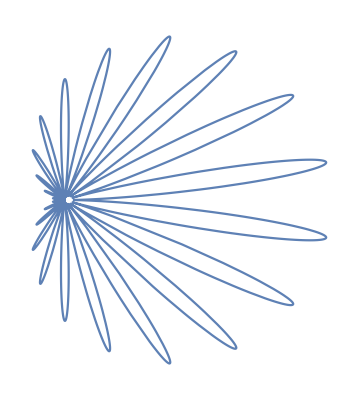

```mathematica
With[{a = 1, b = 1, m1 = 2, m2 = 44,n1 = -0.2, n2 = 1, n3 = 1},Quiet[PolarPlot[Power[Power[Abs[1/a * Cos[(m1/4)*t]],n2]+ Power[Abs[1/b * Sin[(m2/4)*t]],n3],(-1/n1)],{t,0,2*Pi}, Axes -> False]]]
```

## Experiment with the generalized Gielis formula to generate shapes

```mathematica
Manipulate[Quiet[PolarPlot[Power[Power[Abs[1/a * Cos[(m1/4)*t]],n2]+ Power[Abs[1/b * Sin[(m2/4)*t]],n3],(-1/n1)],{t,0,2*Pi}, Axes -> False]], {{a,1},1,10}, {{b,3}, 1,10}, {{m1,2}, -10, 10}, {{m2,2}, -10, 10},{{n1,2}, 1,5}, {{n2,3}, 1, 10}, {{n3,4}, 1,10}, ControlPlacement->Left]
```

## The Gielis formula for 3 dimensional shapes

```mathematica
Manipulate[Quiet[SphericalPlot3D[Power[Power[Abs[1/a * Cos[(m1/4)*t]],n2]+ Power[Abs[1/b * Sin[(m2/4)*t]],n3],(-1/n1)] * Power[Power[Abs[1/a * Cos[(m1/4)*q]],n2]+ Power[Abs[1/b * Sin[(m2/4)*q]],n3],(-1/n1)],{t,-Pi,Pi}, {q,-Pi/2,Pi/2}, Axes -> None, PlotStyle->Directive[LightBlue,Opacity[0.7],Specularity[White,10]],Mesh->All,PlotPoints->30]],{{a,1},1,10}, {{b,3}, 1,10}, {{m1,2}, -10, 10}, {{m2,2}, -10, 10},{{n1,2}, 1,5}, {{n2,3}, 1, 10}, {{n3,4}, 1,10}, ControlPlacement->Left]
```

## Main Function - Creating Gielis shapes

```mathematica
createGellisShape[{a_, b_, m1_,m2_, n1_, n2_, n3_, k_}]:= Module[{},
Quiet[PolarPlot[Power[Power[Abs[1/a * Cos[(m1/4)*t]],n2]+ Power[Abs[1/b * Sin[(m2/4)*t]],n3],(-1/n1)],{t,0,k*Pi}, Axes -> None, ImageSize -> Tiny, PlotStyle-> RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]]]
];
```

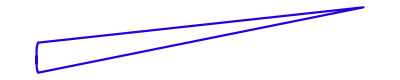
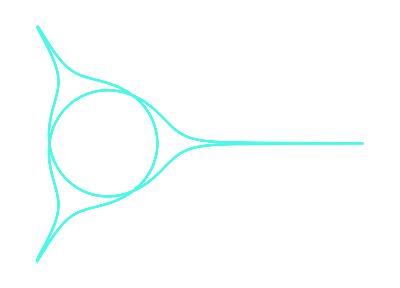

```mathematica
createGellisShape[#] & /@ {{2, 4, -1.5,2,6.2, 8, 10, 5}, {3, 1, 1.5, 3,6.2, 9, 1, 8}}
```

## Generate a number of inputs to the Gielis function

```mathematica
numInputs = 50;
```

```mathematica
gellisInputs = Transpose[{RandomReal[{1,10},numInputs], RandomReal[{1,10},numInputs], RandomReal[{-10,10},numInputs],RandomReal[{-10,10},numInputs], RandomReal[{1,5},numInputs], RandomReal[{1,10},numInputs], RandomReal[{1,10},numInputs], RandomInteger[{1,15},numInputs]}];
```

```mathematica
shapes = Quiet[createGellisShape[#]] & /@ gellisInputs;
```

## Collage of Gielis shapes

```mathematica
ImageCollage[shapes, Background->White]
```

-Graphics-

## Placement of Gellis shapes on a canvas of randomly placed points

```mathematica
rPoints = Table[RandomInteger[100,2],50];
```

```mathematica
g1 = Graphics[Point[rPoints], ImageSize-> 600]
```

-Graphics-

```mathematica
gg1 = Show[g1,Epilog -> Table[{Inset[shapes[[i]], rPoints[[i]]]}, {i,1,50}], ImageSize-> 600, Background-> LightYellow]
```

-Graphics-

```mathematica
gg2 = Show[g1,Epilog -> Inset[shapes[[4]], {50,50}]]
```

-Graphics-

```mathematica
Show[gg1,gg2]
```

-Graphics-

## Place Gellis shapes along curves

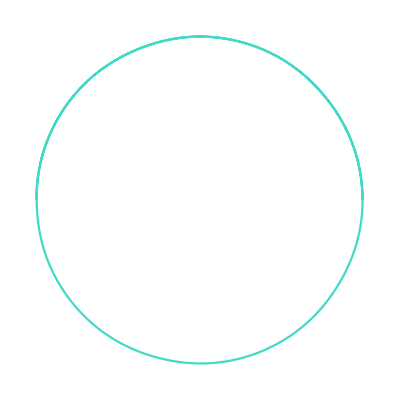
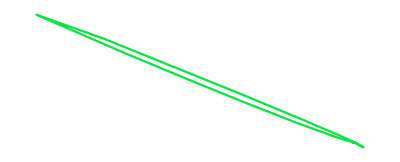

```mathematica
RandomSample[shapes,2]
```

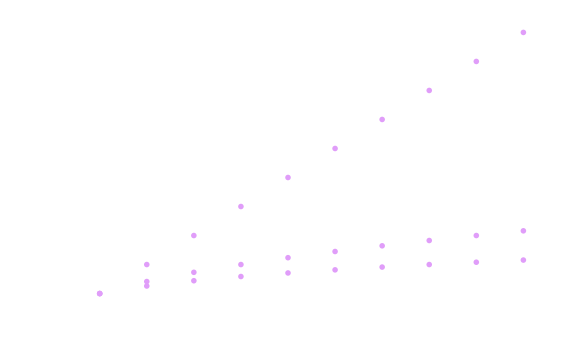

```mathematica
ListPlot[Table[n^(1/p),{p,3},{n,10}],PlotMarkers->RandomSample[shapes,4], ImageSize->Large, Axes -> False, PlotStyle -> RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]]
```

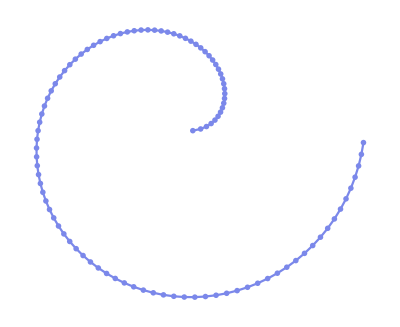

```mathematica
ListPolarPlot[Table[Sqrt[n],{n,100}],Joined->True, PlotMarkers->RandomSample[shapes,1], Axes-> False, PlotStyle-> RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]]
```

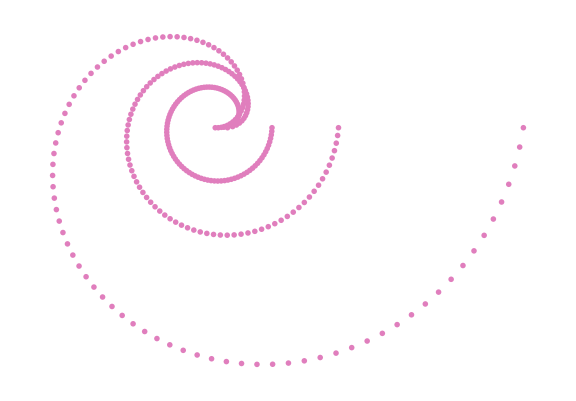

```mathematica
ListPolarPlot[{Range[100]/4,Sqrt[Range[100]],Log[Range[100]]},DataRange->{0,2Pi},PlotMarkers->RandomChoice[shapes,1], ImageSize-> Large, Axes-> False,PlotStyle -> RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]]
```

```mathematica
butterflyOrig[λ_][p_,o___]:=ListPolarPlot[Table[{θ,(Exp[Cos[θ]]-2Cos[4θ])Sin[λ θ]^4},{θ,0,2Pi,p}],o,PlotRange->All,PlotStyle->PointSize[Tiny], ImageSize->Medium];
```

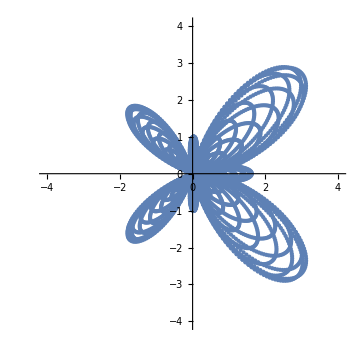

```mathematica
butterflyOrig[99999999][0.00055]
```

```mathematica
butterfly[λ_][p_,o___]:=ListPolarPlot[Table[{θ,(Exp[Cos[θ]]-2Cos[4θ])Sin[λ θ]^4},{θ,0,2Pi,p}],o,PlotRange->All,PlotStyle->PointSize[Tiny], PlotMarkers-> RandomChoice[shapes], Axes -> False, ImageSize->Medium];
```

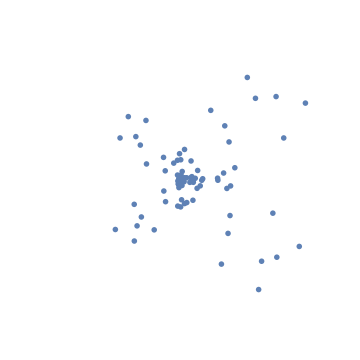
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[butterfly[99999999][0.055], 6]
```